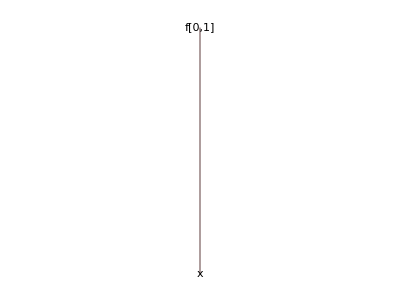

```mathematica
TreeForm[f[0,1][x],1]
```

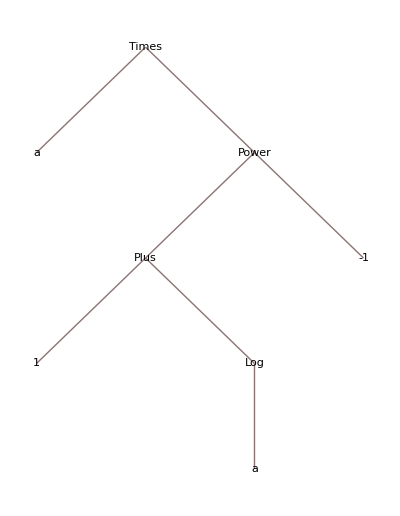

```mathematica
TreeForm[a/(1+Log[a])]
```

### Try to extract the symbol x from each of the following expressions.

```mathematica
Extract[a+b*x,{2,2}]
```

x

```mathematica
Extract[a+b*x[c],{2,2,0}]
```

x

```mathematica
Extract[a+b*x[[c]],{2,2,1}]
```

Part::pkspec1: The expression c cannot be used as a part specification.

x

```mathematica
Extract[x/y,{1}]
```

x

```mathematica
Extract[y/x,{1,1}]
```

x

```mathematica
FullForm[y/x]
```

Times[Power[x,-1],y]

```mathematica
Extract[2^2^x,{2,2}]
```

x

```mathematica
Extract[x[a,b][c],{0,0}]
```

x